### Harmonic oscillator and parabolic 3D particle in magnetic field

```mathematica
{egnVal1,egnVec1}=NDEigensystem[{-1/2 Laplacian[u[x],{x}]+1/2 x^2 u[x]},u[x],{x,0,10},2];

{egnVal2,egnVec2}=NDEigensystem[{-1/2 Laplacian[u[x],{x}]+1/2 x^2 u[x],DirichletCondition[u[x]==0,True]},u[x],{x,0,10},2];
```

```mathematica
egnVal=Riffle[egnVal1,egnVal2]
(*{0.500079,1.50054,2.5019,3.5047}*)
```

{0.500079,1.50054,2.5019,3.5047}

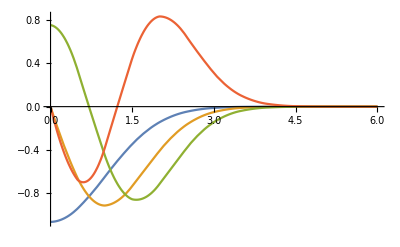

```mathematica
egnVec=Riffle[egnVec1,egnVec2];
Plot[Evaluate[egnVec],{x,0,6},PlotRange->All]
```

#### Landau levels (Landau gauge)

Check for the parabolic dispersion: equidistant energy levels, energy does not depend on p^y

```mathematica
NDEigensystem[-1/2 D[ψ[x], x,x]+1/2(1-x)^2 ψ[x],ψ[x],{x,-10,10},4];
%[[1]]
NDEigensystem[-1/2 D[ψ[x], x,x]+1/2(2-x)^2 ψ[x],ψ[x],{x,-10,10},4];
%[[1]]
```

{0.501189,1.50696,2.53003,3.53334}

{0.501189,1.50696,2.53003,3.53334}

### (Weyl semimetal) Landau levels transition into surface states using the method of mirror images -- SEEMS to be an incorrect approach (because not only wavefunction is continuous across the interface, but its first derivative as well -- this we did not ask for!)

Distances are measured in units of magnetic length, Fermi velocity of the bulk particles is set to 1

For large enough separation of parabolas, states do not talk to each other, zeroth Landua level has zero energy, for non-zero Landau levels there is two-fold degeneracy (so one has to take the appropritate linear superposition of them)

That the eigenvalue of the n=1 level is 2 is in agreement with the expected dispersion relation ϵ = sqrt(pz^2 + 2/l_B^2)

{0.000597761,2.0006,2.28924,4.28924,4.3388}

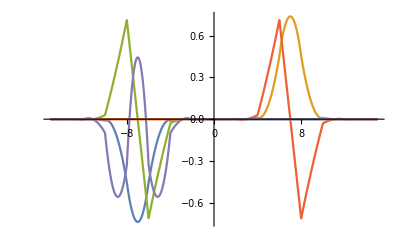

```mathematica
{egnVal1,egnVec1}=NDEigensystem[{-Laplacian[χ[x],{x}]+(Abs[x]-py)^2 χ[x]+Sign[x]χ[x],DirichletCondition[χ[x]==0,True]}/.py->7,χ[x],{x,-20,20},5];
egnVal1
Plot[egnVec1,{x,-15,15},PlotRange->All]
```

But if we make the parabolas closer to each other (and to the surface), the energy of the “zeroth Landau level” goes away from 0, and the energy degeneracy of the higher levels gets broken. At the same time, the energy gap of order 1/l_B between the n=0 and higher levels remains

{0.00261396,1.90001,2.10502}

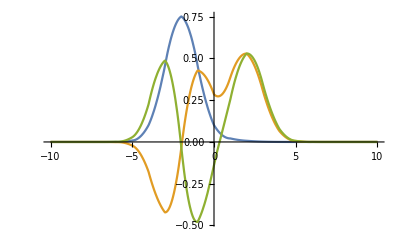

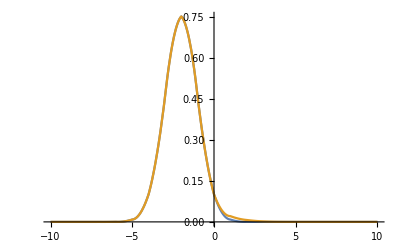

```mathematica
{egnVal1,egnVec1}=NDEigensystem[{-Laplacian[χ[x],{x}]+(Abs[x]-py)^2 χ[x]+Sign[x]χ[x],DirichletCondition[χ[x]==0,True]}/.py->2,χ[x],{x,-10,10},3];
egnVal1
Plot[egnVec1,{x,-10,10},PlotRange->All]

{egnValnoSurface,egnVecnoSurface}=NDEigensystem[{-Laplacian[χ[x],{x}]+(x+py)^2 χ[x]-χ[x],DirichletCondition[χ[x]==0,True]}/.py->2,χ[x],{x,-10,10},1];
Plot[{egnVecnoSurface[[1]],egnVec1[[1]]},{x,-10,10},PlotRange->All]
```

{0.693205,3.12232,4.97719}

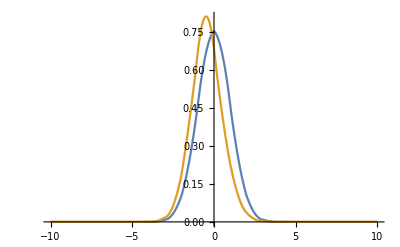

```mathematica
{egnVal1,egnVec1}=NDEigensystem[{-Laplacian[χ[x],{x}]+(Abs[x]-py)^2 χ[x]+Sign[x]χ[x],DirichletCondition[χ[x]==0,True]}/.py->0,χ[x],{x,-10,10},3];
egnVal1

{egnValnoSurface,egnVecnoSurface}=NDEigensystem[{-Laplacian[χ[x],{x}]+(x+py)^2 χ[x]-χ[x],DirichletCondition[χ[x]==0,True]}/.py->0,χ[x],{x,-10,10},1];
Plot[{-egnVecnoSurface[[1]],egnVec1[[1]]},{x,-10,10},PlotRange->All]
```

#### Landau levels transition into surface states using the (Weyl semimetal) : no mirror images

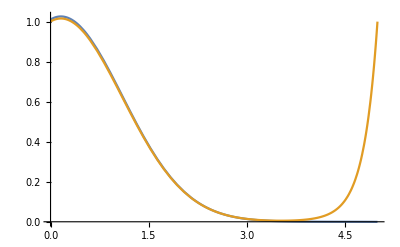

```mathematica
sol1=NDSolve[{-u''[x]+(x^2-1)u[x]==0.2u[x],u[0]==1,u[5]==0},u[x],{x,0,5}];
sol2=NDSolve[{-u''[x]+(x^2-1)u[x]==0.2u[x],u[0]==1,u[5]==1},u[x],{x,0,5}];
Plot[{1.01u[x]/.sol1,u[x]/.sol2},{x,0,5}]
```

```mathematica
NDSolve[{-u''[x]+(x^2-1)u[x]==0.2u[x],u[0]==1,u[5]==0},u[x],{x,0,5}]
```

{{u[x]→InterpolatingFunction[{{0., 5.}}, <>][x]}}

## Landau level -- Fermi arc hybridization in a Weyl semimetal

### BBL set-1 (TODO: include vzcorr in the dispersion relation)

#### BBL parameters

```mathematica
NSolve[{(b0/bz Sin[pz])^2+2Cos[pz](1+M0)-(1+(1+M0)^2-(bz^2-b0^2)/4)==0}/.bz->1.2/.b0->0.2/.M0->-0.3,{pz}]
BBLSubstitution={bz->1.2,b0->0.2,M0->-0.3,pzWR->pz/.%[[1]],ϵ0R->-0.2/1.2 Sin[pz]/.%[[1]],ϵ0L->+0.2/1.2 Sin[pz]/.%[[1]]}
Subscript[v, perp]=Sqrt[4(bz^2-b0^2)/(bz^2-4 ϵ0R^2)]/.BBLSubstitution
Subscript[v, parallel]=1/(2(bz^2-4 ϵ0R^2))Sqrt[2^2(4ϵ0R(1+M0)Sin[pzWR]+b0 bz Cos[pzWR])^2+4(bz^2-4 ϵ0R^2)(4(Sin[pzWR])^2(1+M0)^2-b0^2(Cos[pzWR])^2)]/.BBLSubstitution

vzcorr=(-2(4ϵ0R(1+M0)Sin[pzWR]+b0 bz Cos[pzWR]))/(2(bz^2-4 ϵ0R^2))/.BBLSubstitution
```

NSolve::ifun: Inverse functions are being used by NSolve, so some solutions may not be found; use Reduce for complete solution information.

{{pz→-0.631101},{pz→0.-4.59689 ⅈ},{pz→0.+4.59689 ⅈ},{pz→0.631101}}

{bz→1.2,b0→0.2,M0→-0.3,pzWR→-0.631101,ϵ0R→0.0983391,ϵ0L→-0.0983391}

1.99906

0.684712

-0.0223398

```mathematica
lB=20;
```

#### Dispersion relation of right-chiral surface states

```mathematica
DispersionRelationSurfR=Sqrt[2] Subscript[t, 2] Subscript[v, perp]/lB ParabolicCylinderD[lB^2/Subscript[v, perp]^2((ϵ-ϵ0R)^2-Subscript[v, parallel]^2 dPz^2)/2,Sqrt[2]py lB]+(ϵ-ϵ0R+Subscript[v, parallel] dPz)ParabolicCylinderD[lB^2/Subscript[v, perp]^2((ϵ-ϵ0R)^2-Subscript[v, parallel]^2 dPz^2)/2-1,Sqrt[2]py lB]/.BBLSubstitution/.Subscript[t, 2]->-0.848;
dPzMin=ϵ0R/Subscript[v, parallel]/.BBLSubstitution
```

0.143621

The level bending takes place

```mathematica
FindRoot[DispersionRelationSurfR/.dPz->0.01/.py->-0.3,{ϵ,0.1}];
(ϵ-(ϵ0R-Subscript[v, parallel] dPz))/.dPz->0.01/.BBLSubstitution/.%
FindRoot[DispersionRelationSurfR/.dPz->0.01/.py->-0.2,{ϵ,0.1}];
(ϵ-(ϵ0R-Subscript[v, parallel] dPz))/.dPz->0.01/.BBLSubstitution/.%
FindRoot[DispersionRelationSurfR/.dPz->0.01/.py->-0.1,{ϵ,0.1}];
(ϵ-(ϵ0R-Subscript[v, parallel] dPz))/.dPz->0.01/.BBLSubstitution/.%
```

5.55112×10^-17

5.46363×10^-9

0.000906275

Looks like Fermi arc

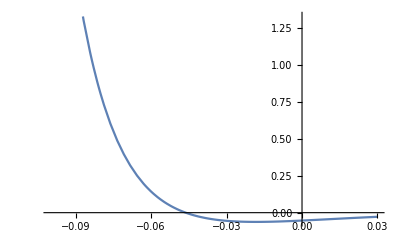

{py→-0.0462608}

```mathematica
Plot[DispersionRelationSurfR/.dPz->0.3/.ϵ->0,{py,-0.1,0.03}]
FindRoot[DispersionRelationSurfR/.dPz->0.3/.ϵ->0,{py,-0.1}]
```

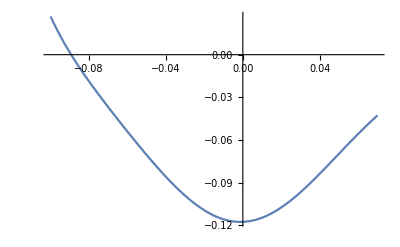

{py→-0.0892967}

```mathematica
Plot[DispersionRelationSurfR/.dPz->0.15/.ϵ->0,{py,-0.1,0.07}]
FindRoot[DispersionRelationSurfR/.dPz->0.15/.ϵ->0,{py,-0.1}]
```

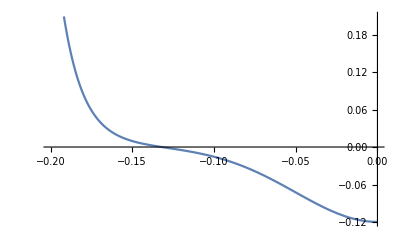

{py→-0.132036}

```mathematica
Plot[DispersionRelationSurfR/.dPz->dPzMin+10^-4/.ϵ->0,{py,-0.2,0}]
FindRoot[DispersionRelationSurfR/.dPz->dPzMin+10^-4/.ϵ->0,{py,-0.1}]
```

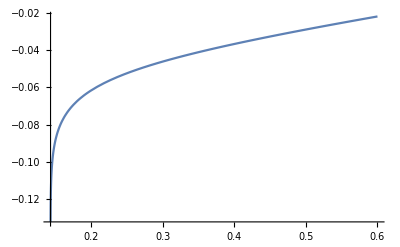

-0.132036

-0.185228

```mathematica
pyFermiR[dPzVar_]:=py/.FindRoot[DispersionRelationSurfR/.dPz->dPzVar/.ϵ->0,{py,-0.1}]
Plot[pyFermiR[dPz],{dPz,dPzMin+10^-4,0.6},PlotRange->All]
pyFermiR[dPzMin+10^-4]
pyFermiR[dPzMin+10^-7]
```

The velocity comes close enough to the expected asymptotic value of the B=0 FAs

-0.650416

-0.648022

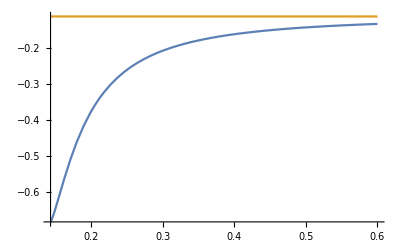

```mathematica
dEOdPzR[dPzVar_,dPzIncrement_]:=ϵ/dPzIncrement/.FindRoot[DispersionRelationSurfR/.dPz->(dPzVar+dPzIncrement)/.py->pyFermiR[dPzVar],{ϵ,0}]
dEOdPzR[0.15,0.001]
dEOdPzR[0.15,0.01]
Plot[{dEOdPzR[dPzVar,10^-4],-(1-Subscript[t, 2]^2)/(1+Subscript[t, 2]^2)Subscript[v, parallel]/.Subscript[t, 2]->-0.848},{dPzVar,dPzMin+10^-5,0.6},PlotRange->All]
```

#### Analysis of the boundary states for left-chiral node

```mathematica
DispersionRelationSurfL=Sqrt[2](-1/Subscript[t, L])Subscript[v, perp]/lB ParabolicCylinderD[lB^2/Subscript[v, perp]^2((ϵ-ϵ0L)^2-Subscript[v, parallel]^2 dPz^2)/2,Sqrt[2]py lB]+(ϵ-ϵ0L-Subscript[v, parallel] dPz)ParabolicCylinderD[lB^2/Subscript[v, perp]^2((ϵ-ϵ0L)^2-Subscript[v, parallel]^2 dPz^2)/2-1,Sqrt[2]py lB]/.BBLSubstitution/.Subscript[t, L]->+0.848;
dPzMax=-ϵ0L/Subscript[v, parallel]/.BBLSubstitution
```

0.143621

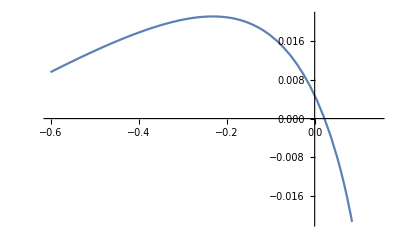

```mathematica
pyFermiL[dPzVar_]:=py/.FindRoot[DispersionRelationSurfL/.dPz->dPzVar/.ϵ->0.,{py,-0.1}]
Plot[pyFermiL[dPz],{dPz,-0.6,dPzMax-10^-3}]
```

```mathematica
dEOdPzL[dPzVar_,dPzIncrement_]:=ϵ/dPzIncrement/.FindRoot[DispersionRelationSurfL/.dPz->(dPzVar+dPzIncrement)/.py->pyFermiL[dPzVar],{ϵ,0}]
dEOdPzL[0.1,-0.001]
dEOdPzL[0.1,-0.01]
```

0.569055

0.565465

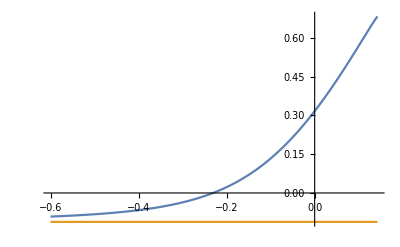

```mathematica
Plot[{dEOdPzL[dPzVar,-0.001],-(1-Subscript[t, 2]^2)/(1+Subscript[t, 2]^2)Subscript[v, parallel]/.Subscript[t, 2]->-0.848},{dPzVar,-0.6,dPzMax-10^-3},PlotRange->All]
```

#### Total contribution of L+R (TO CHECK: does the y-velocity all the time remains positive?)

The (approximate) cancellation happens

```mathematica
Quiet@NIntegrate[dEOdPzR[dPzVar,10^-3],{dPzVar,dPzMin+10^-3,-pzWR/.BBLSubstitution}]
Quiet@NIntegrate[dEOdPzL[dPzVar,-10^-3],{dPzVar,pzWR/.BBLSubstitution,dPzMax-10^-3}]
Quiet@(NIntegrate[dEOdPzR[dPzVar,10^-3],{dPzVar,dPzMin+10^-3,-pzWR/.BBLSubstitution}]+NIntegrate[dEOdPzL[dPzVar,-10^-3],{dPzVar,pzWR/.BBLSubstitution,dPzMax-10^-3}])
```

-0.106448

0.0742305

-0.0322171

How does the answer change if we calculate the derivative wrt p^z with less accuracy?

```mathematica
Quiet@(NIntegrate[dEOdPzR[dPzVar,10^-2],{dPzVar,dPzMin+10^-2,-pzWR/.BBLSubstitution}]+NIntegrate[dEOdPzL[dPzVar,-10^-2],{dPzVar,pzWR/.BBLSubstitution,dPzMax-10^-2}])
```

-0.0334487

How does the answer change if we vary the distribution between the left and right integration limits?

```mathematica
Quiet@(NIntegrate[dEOdPzR[dPzVar,10^-3],{dPzVar,dPzMin+10^-3,-0.1-pzWR/.BBLSubstitution}]+NIntegrate[dEOdPzL[dPzVar,-10^-3],{dPzVar,-0.1+pzWR/.BBLSubstitution,dPzMax-10^-3}])
```

-0.028383

#### Contribution of the n=1 LL (TO REVISE)

Let us shift the chemical potential from ϵ = 0

```mathematica
dPzMax2=0.2;
ϵF2=ϵ0L+Sqrt[Subscript[v, parallel]^2 dPz^2+2 Subscript[v, perp]^2/lB^2]/.dPz->dPzMax2/.BBLSubstitution
ϵ0L+Sqrt[2 2 Subscript[v, perp]^2/lB^2]/.dPz->0.1/.BBLSubstitution
```

0.0984715

0.101567

Only n=0 LL crosses the Fermi level

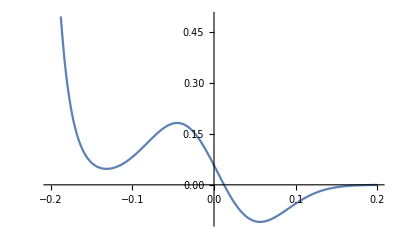

```mathematica
Plot[DispersionRelationSurfL/.dPz->dPzMax2+10^-3/.ϵ->ϵF2,{py,-0.2,0.2}]
```

n=1 LL just starts to cross the Fermi level

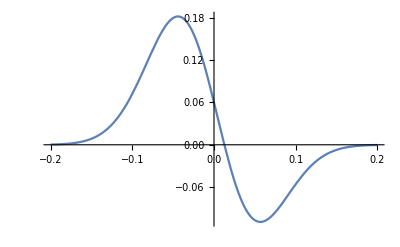

```mathematica
Plot[DispersionRelationSurfL/.dPz->dPzMax2/.ϵ->ϵF2,{py,-0.2,0.2}]
```

Both n=0 and n=1 LLs cross the Fermi level

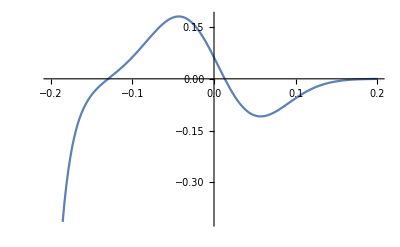

```mathematica
Plot[DispersionRelationSurfL/.dPz->dPzMax2-10^-3/.ϵ->ϵF2,{py,-0.2,0.2}]
```

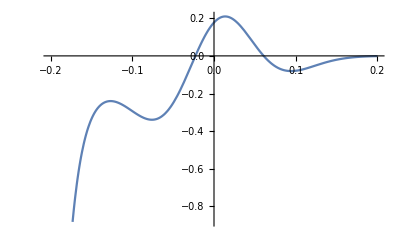

```mathematica
Plot[DispersionRelationSurfL/.dPz->0./.ϵ->ϵF2,{py,-0.2,0.2}]
```

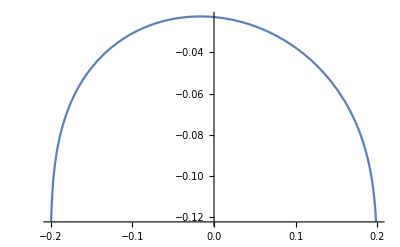

```mathematica
pyFermiL2[dPzVar_]:=py/.FindRoot[DispersionRelationSurfL/.dPz->dPzVar/.ϵ->ϵF2,{py,-0.05}]
Plot[pyFermiL2[dPz],{dPz,-dPzMax2,dPzMax2}]
```

```mathematica
dEOdPzL2[dPzVar_,dPzIncrement_]:=(ϵ-ϵF2)/dPzIncrement/.FindRoot[DispersionRelationSurfL/.dPz->(dPzVar+dPzIncrement)/.py->pyFermiL2[dPzVar],{ϵ,ϵF2}]
dEOdPzL2[0.06,-0.0001]
dEOdPzL2[0.06,-0.001]
```

0.17753

0.176554

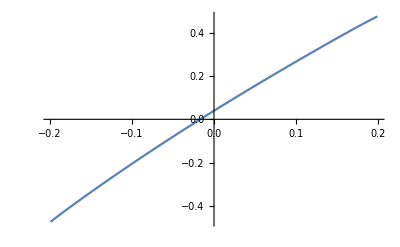

0.010935

0.0109708

```mathematica
Plot[dEOdPzL2[dPzVar,-10^-4],{dPzVar,-dPzMax2+10^-3,dPzMax2-10^-3}]
Quiet@NIntegrate[dEOdPzL2[dPzVar,-10^-4],{dPzVar,-dPzMax2+10^-3,dPzMax2-10^-3}]
Quiet@NIntegrate[dEOdPzL2[dPzVar,-10^-5],{dPzVar,-dPzMax2+10^-3,dPzMax2-10^-3}]
```

## BBL set-2

#### Set-2 parameters

```mathematica
NSolve[{(b0/bz Sin[pz])^2+2Cos[pz](1+M0)-(1+(1+M0)^2-(bz^2-b0^2)/4)==0}/.bz->1.2/.b0->0.1/.M0->-0.3,{pz}]
BBLSet2={bz->1.2,b0->0.1,M0->-0.3,pzWR->pz/.%[[1]],ϵ0R->-0.1/1.2 Sin[pz]/.%[[1]],ϵ0L->+0.1/1.2 Sin[pz]/.%[[1]]}
Subscript[vSet2, perp]=Sqrt[4(bz^2-b0^2)/(bz^2-4 ϵ0R^2)]/.BBLSet2
Subscript[vSet2, parallel]=1/(2(bz^2-4 ϵ0R^2))Sqrt[2^2(4ϵ0R(1+M0)Sin[pzWR]+b0 bz Cos[pzWR])^2+4(bz^2-4 ϵ0R^2)(4(Sin[pzWR])^2(1+M0)^2-b0^2(Cos[pzWR])^2)]/.BBLSet2
vzcorrSet2=(-(4ϵ0R(1+M0)Sin[pzWR]+b0 bz Cos[pzWR]))/(bz^2-4 ϵ0R^2)/.BBLSet2
dPzMinSet2=ϵ0R/(Subscript[vSet2, parallel]-vzcorrSet2)/.BBLSet2
dPzMaxSet2=-ϵ0L/(Subscript[vSet2, parallel]+vzcorrSet2)/.BBLSet2
```

NSolve::ifun: Inverse functions are being used by NSolve, so some solutions may not be found; use Reduce for complete solution information.

{{pz→-0.631403},{pz→0.-5.99541 ⅈ},{pz→0.+5.99541 ⅈ},{pz→0.631403}}

{bz→1.2,b0→0.1,M0→-0.3,pzWR→-0.631403,ϵ0R→0.0491898,ϵ0L→-0.0491898}

1.99978

0.687765

-0.0108816

0.0704073

0.072671

```mathematica
(*This value of Subscript[t, R] was found in Vazifeh-Franz.nb*)
tRSet2=-0.92;
tLSet2=-tRSet2;
(*This is the parameter that enters Energy = ... + vzQuadraticCorrectionSet2×pz^3 *)
lB=50;
```

The values of velocity agree with KWANT, provided that we choose proper vzQuadraticCorrectionSet2

```mathematica
(*So far, the parameter is extracted manually from KWANT, and in principle it can depend on the boundary condition, in particular on tRSet2*)
vzQuadraticCorrectionSet2 = -1.3×10^-2;
-(1-tRSet2^2)/(1+tRSet2^2)Subscript[vSet2, parallel]+vzcorrSet2
-(1-tRSet2^2)/(1+tRSet2^2)Subscript[vSet2, parallel]+vzcorrSet2+3vzQuadraticCorrectionSet2 dPz^2/.dPz->pzWR/.BBLSet2
```

-0.0680961

-0.0836442

#### Dispersion relation of right-chiral states

```mathematica
DispersionRSet2=Sqrt[2]tRSet2 Subscript[vSet2, perp]/lB ParabolicCylinderD[lB^2/Subscript[vSet2, perp]^2(δϵ^2-Subscript[vSet2, parallel]^2 dPz^2)/2,Sqrt[2]py lB]+(δϵ+Subscript[vSet2, parallel] dPz)ParabolicCylinderD[lB^2/Subscript[vSet2, perp]^2(δϵ^2-Subscript[vSet2, parallel]^2 dPz^2)/2-1,Sqrt[2]py lB]/.δϵ->ϵ-ϵ0R-vzcorrSet2 dPz-vzQuadraticCorrectionSet2 dPz^3/.BBLSet2;
```

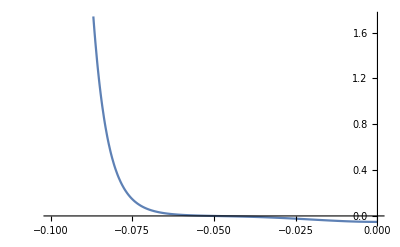

{py→-0.0502242}

```mathematica
Plot[DispersionRSet2/.dPz->dPzMinSet2+10^-4/.ϵ->0,{py,-0.1,0}]
FindRoot[DispersionRSet2/.dPz->dPzMinSet2+10^-4/.ϵ->0,{py,-0.1}]
```

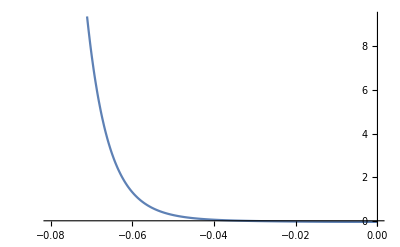

{py→-0.0326948}

```mathematica
Plot[DispersionRSet2/.dPz->0.08/.ϵ->0,{py,-0.08,0}]
FindRoot[DispersionRSet2/.dPz->0.08/.ϵ->0,{py,-0.1}]
```

Looks like Fermi arc

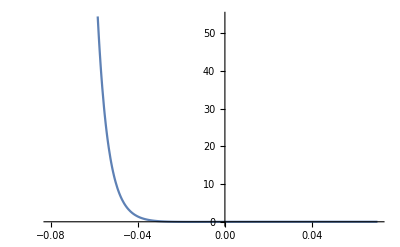

{py→-0.0236644}

```mathematica
Plot[DispersionRSet2/.dPz->0.15/.ϵ->0,{py,-0.08,0.07}]
FindRoot[DispersionRSet2/.dPz->0.15/.ϵ->0,{py,-0.1}]
```

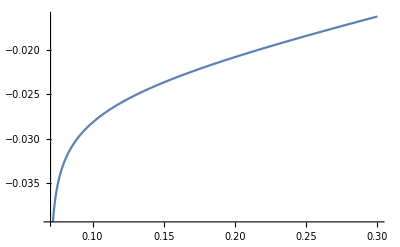

-0.0502242

-0.0597398

```mathematica
pyFermiRSet2[dPzVar_]:=py/.FindRoot[DispersionRSet2/.dPz->dPzVar/.ϵ->0,{py,-0.1}]
Plot[pyFermiRSet2[dPzVar],{dPzVar,dPzMinSet2+10^-4,0.3}]
pyFermiRSet2[dPzMinSet2+10^-4]
pyFermiRSet2[dPzMinSet2+10^-7]
```

-0.128802

-0.125072

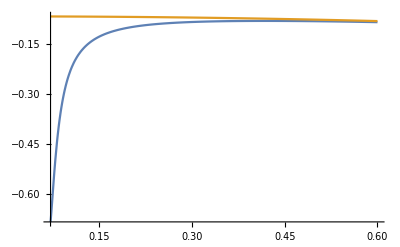

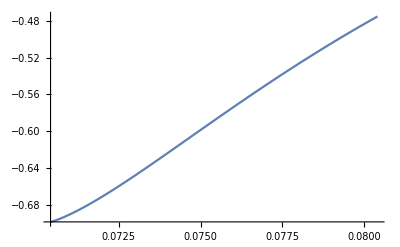

```mathematica
dEOdPzRSet2[dPzVar_,dPzIncrement_]:=ϵ/dPzIncrement/.FindRoot[DispersionRSet2/.dPz->(dPzVar+dPzIncrement)/.py->pyFermiRSet2[dPzVar],{ϵ,0}]
dEOdPzRSet2[0.15,0.001]
dEOdPzRSet2[0.15,0.01]
Plot[{dEOdPzRSet2[dPzVar,0.001],-(1-tRSet2^2)/(1+tRSet2^2)Subscript[vSet2, parallel]+vzcorrSet2+3vzQuadraticCorrectionSet2 dPzVar^2},{dPzVar,dPzMinSet2+10^-3,0.6},PlotRange->All]
Plot[dEOdPzRSet2[dPzVar,10^-4],{dPzVar,dPzMinSet2+10^-5,dPzMinSet2+10^-2}]
```

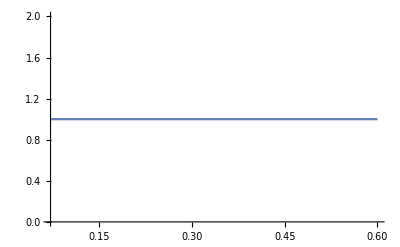

```mathematica
SignRSet2[dPzVar_]:=Sign[ϵ]/.FindRoot[DispersionRSet2/.dPz->dPzVar/.py->pyFermiRSet2[dPzVar]+10^-3,{ϵ,0}]
Plot[SignRSet2[dPzVar],{dPzVar,dPzMinSet2+10^-3,0.6},PlotRange->All]
```

#### Left chirality

```mathematica
DispersionLSet2=Sqrt[2](-1/tLSet2)Subscript[vSet2, perp]/lB ParabolicCylinderD[lB^2/Subscript[vSet2, perp]^2(δϵ^2-Subscript[vSet2, parallel]^2 dPz^2)/2,Sqrt[2]py lB]+(δϵ-Subscript[vSet2, parallel] dPz)ParabolicCylinderD[lB^2/Subscript[vSet2, perp]^2(δϵ^2-Subscript[vSet2, parallel]^2 dPz^2)/2-1,Sqrt[2]py lB]/.δϵ->ϵ-ϵ0L-vzcorrSet2 dPz-vzQuadraticCorrectionSet2 dPz^3/.BBLSet2;
```

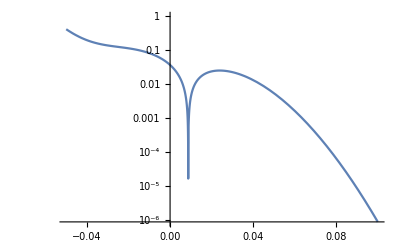

{py→0.00874329}

```mathematica
LogPlot[Abs[DispersionLSet2]/.dPz->0./.ϵ->0,{py,-0.05,0.1}]
FindRoot[DispersionLSet2/.dPz->0./.ϵ->0,{py,-0.01}]
```

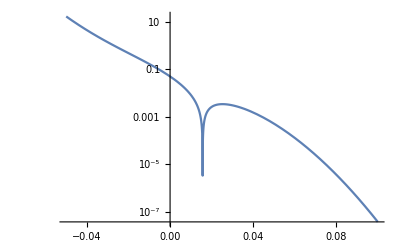

{py→0.0156826}

```mathematica
LogPlot[Abs[DispersionLSet2]/.dPz->-0.1/.ϵ->0,{py,-0.05,0.1}]
FindRoot[DispersionLSet2/.dPz->-0.1/.ϵ->0,{py,-0.01}]
```

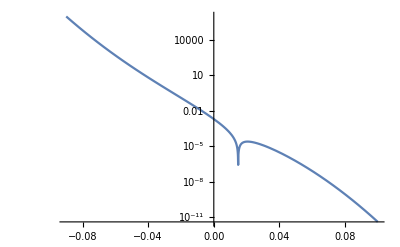

{py→0.0148529}

```mathematica
LogPlot[Abs[DispersionLSet2]/.dPz->-0.2/.ϵ->0,{py,-0.09,0.1}]
FindRoot[DispersionLSet2/.dPz->-0.2/.ϵ->0,{py,-0.01}]
```

Why p^yF is non-monotonic?

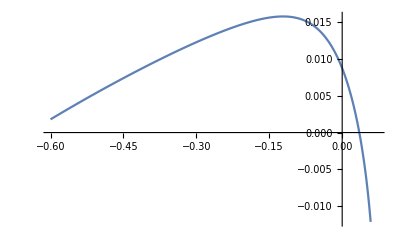

```mathematica
pyFermiLSet2[dPzVar_]:=py/.FindRoot[DispersionLSet2/.dPz->dPzVar/.ϵ->0,{py,-0.01}]
Plot[pyFermiLSet2[dPzVar],{dPzVar,-0.6,dPzMaxSet2-10^-4}]
```

0.115939

0.12735

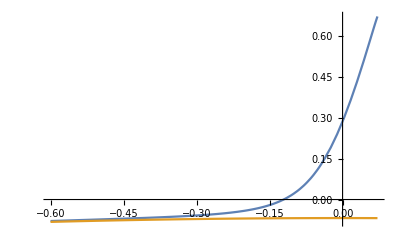

```mathematica
dEOdPzLSet2[dPzVar_,dPzIncrement_]:=ϵ/dPzIncrement/.FindRoot[DispersionLSet2/.dPz->(dPzVar+dPzIncrement)/.py->pyFermiLSet2[dPzVar],{ϵ,0}]
dEOdPzLSet2[-0.05,0.001]
dEOdPzLSet2[-0.05,0.01]
Plot[{dEOdPzLSet2[dPzVar,-0.001],-(1-tLSet2^2)/(1+tLSet2^2)Subscript[vSet2, parallel]+vzcorrSet2+3vzQuadraticCorrectionSet2 dPzVar^2},{dPzVar,-0.6,dPzMaxSet2-10^-3},PlotRange->All]
```

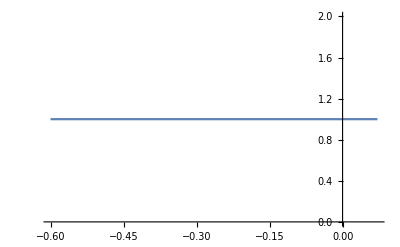

```mathematica
SignLSet2[dPzVar_]:=Sign[ϵ]/.FindRoot[DispersionLSet2/.dPz->dPzVar/.py->pyFermiLSet2[dPzVar]+10^-3,{ϵ,0}]
Plot[SignLSet2[dPzVar],{dPzVar,-0.6,dPzMaxSet2-10^-3},PlotRange->All]
```

#### Total contribution of L+R to the current

```mathematica
IZRSet2=Quiet@NIntegrate[SignRSet2[dPzVar] dEOdPzRSet2[dPzVar,10^-3],{dPzVar,dPzMinSet2+10^-3,-pzWR/.BBLSet2}]
IZLSet2=Quiet@NIntegrate[SignLSet2[dPzVar]dEOdPzLSet2[dPzVar,-10^-3],{dPzVar,pzWR/.BBLSet2,dPzMaxSet2-10^-3}]
IZRSet2+IZLSet2
```

-0.0626142

0.0162444

-0.0463697

While the BBL’16 gives the prefactor close to

```mathematica
-ϵ0R/.BBLSet2
```

-0.0491898

Reducing the precision in the calculation of the z-velocity does not change the result significantly

```mathematica
temp280117=Quiet@NIntegrate[SignRSet2[dPzVar] dEOdPzRSet2[dPzVar,10^-2],{dPzVar,dPzMinSet2+10^-3,-pzWR/.BBLSet2}]
Quiet@NIntegrate[SignLSet2[dPzVar]dEOdPzLSet2[dPzVar,-10^-2],{dPzVar,pzWR/.BBLSet2,dPzMaxSet2-10^-3}]
temp280117+%
```

-0.0611597

0.013955

-0.0472046

#### Calculation restricted to the domain of the minimal effective theory (minimal in the sense that vzQuadratic=0) + assumption of the p^y- p^z separability of the FA energy: again we are close to -1/2!

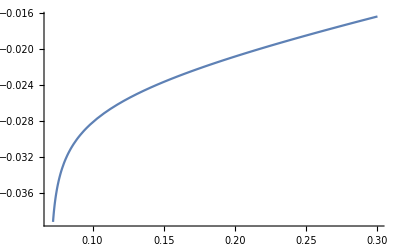

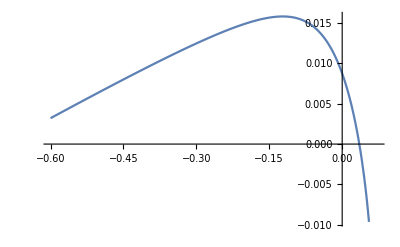

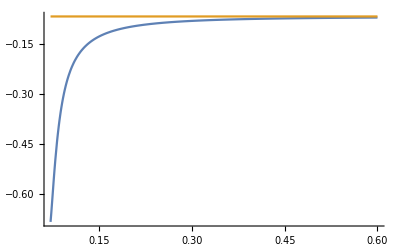

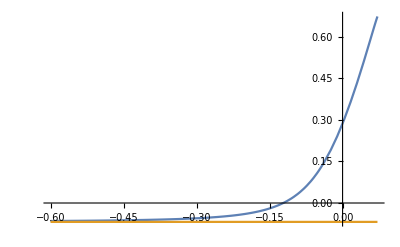

```mathematica
DispersionRMinSet2=Sqrt[2]tRSet2 Subscript[vSet2, perp]/lB ParabolicCylinderD[lB^2/Subscript[vSet2, perp]^2(δϵ^2-Subscript[vSet2, parallel]^2 dPz^2)/2,Sqrt[2]py lB]+(δϵ+Subscript[vSet2, parallel] dPz)ParabolicCylinderD[lB^2/Subscript[vSet2, perp]^2(δϵ^2-Subscript[vSet2, parallel]^2 dPz^2)/2-1,Sqrt[2]py lB]/.δϵ->ϵ-ϵ0R-vzcorrSet2 dPz/.BBLSet2;
DispersionLMinSet2=Sqrt[2](-1/tLSet2)Subscript[vSet2, perp]/lB ParabolicCylinderD[lB^2/Subscript[vSet2, perp]^2(δϵ^2-Subscript[vSet2, parallel]^2 dPz^2)/2,Sqrt[2]py lB]+(δϵ-Subscript[vSet2, parallel] dPz)ParabolicCylinderD[lB^2/Subscript[vSet2, perp]^2(δϵ^2-Subscript[vSet2, parallel]^2 dPz^2)/2-1,Sqrt[2]py lB]/.δϵ->ϵ-ϵ0L-vzcorrSet2 dPz/.BBLSet2;
pyFermiRMinSet2[dPzVar_]:=py/.FindRoot[DispersionRMinSet2/.dPz->dPzVar/.ϵ->0,{py,-0.1}]
Plot[pyFermiRMinSet2[dPzVar],{dPzVar,dPzMinSet2+10^-4,0.3}]
pyFermiLMinSet2[dPzVar_]:=py/.FindRoot[DispersionLMinSet2/.dPz->dPzVar/.ϵ->0,{py,-0.01}]
Plot[pyFermiLMinSet2[dPzVar],{dPzVar,-0.6,dPzMaxSet2-10^-4}]
dEOdPzRMinSet2[dPzVar_,dPzIncrement_]:=ϵ/dPzIncrement/.FindRoot[DispersionRMinSet2/.dPz->(dPzVar+dPzIncrement)/.py->pyFermiRMinSet2[dPzVar],{ϵ,0}]
Plot[{dEOdPzRMinSet2[dPzVar,0.001],-(1-tRSet2^2)/(1+tRSet2^2)Subscript[vSet2, parallel]+vzcorrSet2},{dPzVar,dPzMinSet2+10^-3,0.6},PlotRange->All]
dEOdPzLMinSet2[dPzVar_,dPzIncrement_]:=ϵ/dPzIncrement/.FindRoot[DispersionLMinSet2/.dPz->(dPzVar+dPzIncrement)/.py->pyFermiLMinSet2[dPzVar],{ϵ,0}]
Plot[{dEOdPzLMinSet2[dPzVar,-0.001],-(1-tLSet2^2)/(1+tLSet2^2)Subscript[vSet2, parallel]+vzcorrSet2},{dPzVar,-0.6,dPzMaxSet2-10^-3},PlotRange->All]
```

Now we calculate the current in the effective theory, and for the UV-completion we say that the FA energy is SEPARABLE into the sum of functions of py and pz only

```mathematica
dPzCutR=0.3;
dPzCutL=-0.3;
IZRCutSet2=Quiet@NIntegrate[dEOdPzRMinSet2[dPzVar,10^-3],{dPzVar,dPzMinSet2+10^-3,dPzCutR}];
IZLCutSet2=Quiet@NIntegrate[dEOdPzLMinSet2[dPzVar,-10^-3],{dPzVar,dPzCutL,dPzMaxSet2-10^-3}];
IZRCutSet2+IZLCutSet2+(ϵ0L+(-(1-tRSet2^2)/(1+tRSet2^2)Subscript[vSet2, parallel]+vzcorrSet2)dPzCutL)-(ϵ0R+(-(1-tRSet2^2)/(1+tRSet2^2)Subscript[vSet2, parallel]+vzcorrSet2)dPzCutR)/.BBLSet2;
%/-ϵ0R/.BBLSet2
```

1.06101

The integral does not get changed significantly if we reduce the precision:

1) if we cut more of the effective-theory region

```mathematica
dPzCutR=0.2;
dPzCutL=-0.2;
IZRCutSet2=Quiet@NIntegrate[dEOdPzRMinSet2[dPzVar,10^-3],{dPzVar,dPzMinSet2+10^-3,dPzCutR}]
IZLCutSet2=Quiet@NIntegrate[dEOdPzLMinSet2[dPzVar,-10^-3],{dPzVar,dPzCutL,dPzMaxSet2-10^-3}]
IZRCutSet2+IZLCutSet2+(ϵ0L+(-(1-tRSet2^2)/(1+tRSet2^2)Subscript[vSet2, parallel]+vzcorrSet2)dPzCutL)-(ϵ0R+(-(1-tRSet2^2)/(1+tRSet2^2)Subscript[vSet2, parallel]+vzcorrSet2)dPzCutR)/.BBLSet2
```

-0.0258763

0.0449177

-0.0520999

2) if we change the differentiation step

```mathematica
dPzCutR=0.3;
dPzCutL=-0.3;
IZRCutSet2=Quiet@NIntegrate[dEOdPzRMinSet2[dPzVar,10^-2],{dPzVar,dPzMinSet2+10^-2,dPzCutR}]
IZLCutSet2=Quiet@NIntegrate[dEOdPzLMinSet2[dPzVar,-10^-2],{dPzVar,dPzCutL,dPzMaxSet2-10^-2}]
IZRCutSet2+IZLCutSet2+(ϵ0L+(-(1-tRSet2^2)/(1+tRSet2^2)Subscript[vSet2, parallel]+vzcorrSet2)dPzCutL)-(ϵ0R+(-(1-tRSet2^2)/(1+tRSet2^2)Subscript[vSet2, parallel]+vzcorrSet2)dPzCutR)/.BBLSet2
```

-0.0283206

0.0320645

-0.053778

#### Calculation of I^z in the effective theory with DEFORMED boundary condition: the prefactor is different by about two times! (Separable approximation)

The total velocity of the Fermi arc in the vicinity of a node was extracted from KWANT (the on-site Hamiltonians of the boundary and the next-to-boundary sites were rescaled by 3 times)

```mathematica
vzArcTotBoundDef=0.44;
tRSet2BoundDef=-Sqrt[(Subscript[vSet2, parallel]-(vzcorrSet2-vzArcTotBoundDef))/(Subscript[vSet2, parallel]+(vzcorrSet2-vzArcTotBoundDef))]
tLSet2BoundDef=-tRSet2BoundDef;
```

-2.19244

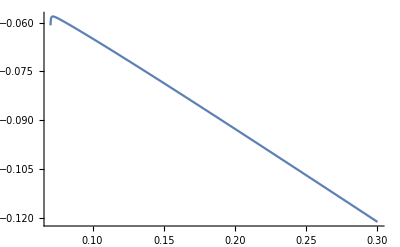

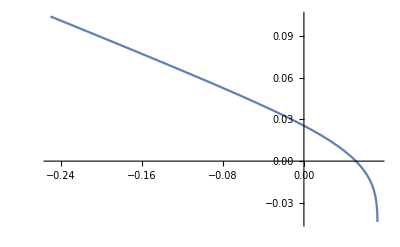

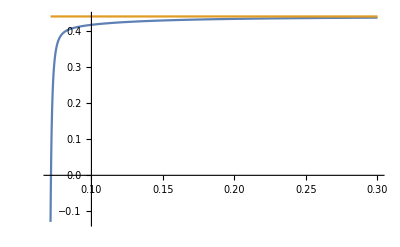

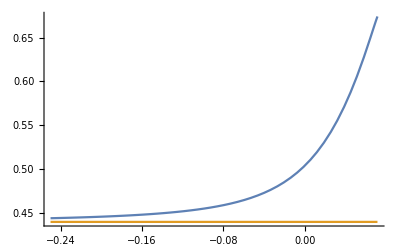

```mathematica
DispersionRMinSet2BoundDef=Sqrt[2]tRSet2BoundDef Subscript[vSet2, perp]/lB ParabolicCylinderD[lB^2/Subscript[vSet2, perp]^2(δϵ^2-Subscript[vSet2, parallel]^2 dPz^2)/2,Sqrt[2]py lB]+(δϵ+Subscript[vSet2, parallel] dPz)ParabolicCylinderD[lB^2/Subscript[vSet2, perp]^2(δϵ^2-Subscript[vSet2, parallel]^2 dPz^2)/2-1,Sqrt[2]py lB]/.δϵ->ϵ-ϵ0R-vzcorrSet2 dPz/.BBLSet2;
DispersionLMinSet2BoundDef=Sqrt[2](-1/tLSet2BoundDef)Subscript[vSet2, perp]/lB ParabolicCylinderD[lB^2/Subscript[vSet2, perp]^2(δϵ^2-Subscript[vSet2, parallel]^2 dPz^2)/2,Sqrt[2]py lB]+(δϵ-Subscript[vSet2, parallel] dPz)ParabolicCylinderD[lB^2/Subscript[vSet2, perp]^2(δϵ^2-Subscript[vSet2, parallel]^2 dPz^2)/2-1,Sqrt[2]py lB]/.δϵ->ϵ-ϵ0L-vzcorrSet2 dPz/.BBLSet2;
pyFermiRMinSet2BoundDef[dPzVar_]:=py/.FindRoot[DispersionRMinSet2BoundDef/.dPz->dPzVar/.ϵ->0,{py,-0.2,0.1},Method->"Brent"]
Plot[pyFermiRMinSet2BoundDef[dPzVar],{dPzVar,dPzMinSet2+10^-4,0.3}]
pyFermiLMinSet2BoundDef[dPzVar_]:=py/.FindRoot[DispersionLMinSet2BoundDef/.dPz->dPzVar/.ϵ->0,{py,-0.1,0.15},Method->"Brent"]
Plot[pyFermiLMinSet2BoundDef[dPzVar],{dPzVar,-0.25,dPzMaxSet2-10^-4}]
dEOdPzRMinSet2BoundDef[dPzVar_,dPzIncrement_]:=ϵ/dPzIncrement/.FindRoot[DispersionRMinSet2BoundDef/.dPz->(dPzVar+dPzIncrement)/.py->pyFermiRMinSet2BoundDef[dPzVar],{ϵ,0}]
Plot[{dEOdPzRMinSet2BoundDef[dPzVar,0.001],-(1-tRSet2BoundDef^2)/(1+tRSet2BoundDef^2)Subscript[vSet2, parallel]+vzcorrSet2},{dPzVar,dPzMinSet2+10^-3,0.3},PlotRange->All]
dEOdPzLMinSet2BoundDef[dPzVar_,dPzIncrement_]:=ϵ/dPzIncrement/.FindRoot[DispersionLMinSet2BoundDef/.dPz->(dPzVar+dPzIncrement)/.py->pyFermiLMinSet2BoundDef[dPzVar],{ϵ,0}]
Plot[{dEOdPzLMinSet2BoundDef[dPzVar,-0.001],-(1-tLSet2BoundDef^2)/(1+tLSet2BoundDef^2)Subscript[vSet2, parallel]+vzcorrSet2},{dPzVar,-0.25,dPzMaxSet2-10^-3},PlotRange->All]
```

```mathematica
dPzCutRBoundDef=0.3;
dPzCutLBoundDef=-0.25;
IZRCutSet2BoundDef=Quiet@NIntegrate[dEOdPzRMinSet2BoundDef[dPzVar,10^-3],{dPzVar,dPzMinSet2+10^-3,dPzCutRBoundDef}];
IZLCutSet2BoundDef=Quiet@NIntegrate[dEOdPzLMinSet2BoundDef[dPzVar,-10^-3],{dPzVar,dPzCutLBoundDef,dPzMaxSet2-10^-3}];
IZRCutSet2BoundDef+IZLCutSet2BoundDef+(ϵ0L+(-(1-tRSet2BoundDef^2)/(1+tRSet2BoundDef^2)Subscript[vSet2, parallel]+vzcorrSet2)dPzCutLBoundDef)-(ϵ0R+(-(1-tRSet2BoundDef^2)/(1+tRSet2BoundDef^2)Subscript[vSet2, parallel]+vzcorrSet2)dPzCutRBoundDef)/.BBLSet2;
%/-ϵ0R/.BBLSet2
```

1.78485

Reduction of the p^z-range of the effective theory does not change the result significantly

```mathematica
dPzCutRBoundDef=0.2;
dPzCutLBoundDef=-0.15;
IZRCutSet2BoundDef=Quiet@NIntegrate[dEOdPzRMinSet2BoundDef[dPzVar,10^-3],{dPzVar,dPzMinSet2+10^-3,dPzCutRBoundDef}]
IZLCutSet2BoundDef=Quiet@NIntegrate[dEOdPzLMinSet2BoundDef[dPzVar,-10^-3],{dPzVar,dPzCutLBoundDef,dPzMaxSet2-10^-3}]
IZRCutSet2BoundDef+IZLCutSet2BoundDef+(ϵ0L+(-(1-tRSet2BoundDef^2)/(1+tRSet2BoundDef^2)Subscript[vSet2, parallel]+vzcorrSet2)dPzCutLBoundDef)-(ϵ0R+(-(1-tRSet2BoundDef^2)/(1+tRSet2BoundDef^2)Subscript[vSet2, parallel]+vzcorrSet2)dPzCutRBoundDef)/.BBLSet2
```

0.053611

0.110828

-0.0879409

Reduction of the precision in calculation of the z-velocity also does not alter the result significantly

```mathematica
dPzCutRBoundDef=0.3;
dPzCutLBoundDef=-0.25;
IZRCutSet2BoundDef=Quiet@NIntegrate[dEOdPzRMinSet2BoundDef[dPzVar,10^-2],{dPzVar,dPzMinSet2+10^-3,dPzCutRBoundDef}]
IZLCutSet2BoundDef=Quiet@NIntegrate[dEOdPzLMinSet2BoundDef[dPzVar,-10^-2],{dPzVar,dPzCutLBoundDef,dPzMaxSet2-10^-3}]
IZRCutSet2BoundDef+IZLCutSet2BoundDef+(ϵ0L+(-(1-tRSet2BoundDef^2)/(1+tRSet2BoundDef^2)Subscript[vSet2, parallel]+vzcorrSet2)dPzCutLBoundDef)-(ϵ0R+(-(1-tRSet2BoundDef^2)/(1+tRSet2BoundDef^2)Subscript[vSet2, parallel]+vzcorrSet2)dPzCutRBoundDef)/.BBLSet2
```

0.0978663

0.155147

-0.0873665

#### Estimate of the non-separability of the FA dispersion in the UV region, and its influence on the I^z prefactor: the “correction” does not seem to be small

The polynomial expansion of the FA dispersion to the low orders in p^z is NOT ENOUGH

Let us do instead direct interpolation in Mathematica, without using polynomials

```mathematica
f1=Interpolation[{{0.,0.},{-0.1,0.02222189},{0.1,-0.02222189},{-0.2,0.04154513},{0.2,-0.04154513},{-0.3,0.05416651},{0.3,-0.05416651},{-0.4,0.0577292},{0.4,-0.0577292},{-0.5,0.05482147},{0.5,-0.05482147},{-0.6,0.05037931 },{-0.61,0.04998335},{-0.62,0.0496031}}]
f1[-0.001]
(*While the numerical value for pz = -0.001 is 2.26489015 10^-4 *)
f1[-0.631]
Needs["NumericalCalculus`"]
(*The z-velocity is close to the numerically extracted value of around 0.04*)
ND[f1[pz],pz,-0.631]
```

InterpolatingFunction[{{-0.62, 0.5}}, <>]

0.00022705

InterpolatingFunction::dmval: Input value {-0.631} lies outside the range of data in the interpolating function. Extrapolation will be used.

0.049205

InterpolatingFunction::dmval: Input value {-0.631} lies outside the range of data in the interpolating function. Extrapolation will be used.

0.0351045

InterpolatingFunction[{{-0.61, 0.}}, <>]

InterpolatingFunction::dmval: Input value {-0.631} lies outside the range of data in the interpolating function. Extrapolation will be used.

{1.98872,1.99451}

InterpolatingFunction::dmval: Input value {-0.629987} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

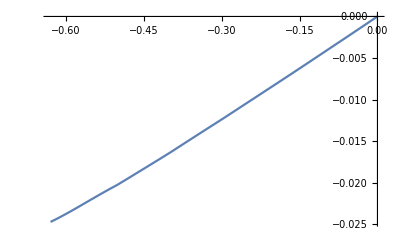

InterpolatingFunction::dmval: Input value {-0.629987} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

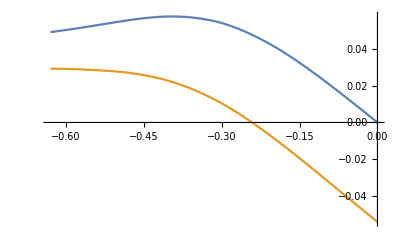

0.00795031

```mathematica
pyInterpol=0.01;
fTemp16022017=Interpolation[{{0.,0.05415455},{-0.1,0.07547719},{-0.2,0.09157841},{-0.3,0.09791217},{-0.4,0.09295072},{-0.5,0.08194527},{-0.6,0.07159381},{-0.61,0.07073612}}]
f2[x_]:=(fTemp16022017[x]-f1[x])/pyInterpol
{f2[-0.631],-(2tRSet2BoundDef)/(1+tRSet2BoundDef^2)Subscript[vSet2, perp]}
Plot[-f1[pz]/f2[pz],{pz,-0.63,0.}]
Plot[{f1[pz],f1[pz]-0.01 f2[pz]},{pz,-0.63,0.}]
f1[-0.6]-0.02 f2[-0.6]
(*While KWANT gives for pz=-0.6 and py=-0.02 value 0.08691175, which is 10% off, so py^2 and higher-order corrections in py seem to be NOT important*)
```

The correction to the I^z prefactor has the same sign as the value calculated in the separable approximation

InterpolatingFunction::dmval: Input value {-0.630987} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

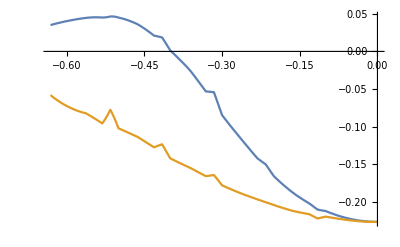

-0.104286

-0.0178771

```mathematica
Plot[{ND[f1[pzVar],pzVar,pz],ND[f1[pzVar],pzVar,pz]-f1[pz]/f2[pz] ND[f2[pzVar],pzVar,pz]},{pz,-0.631,0.}]
2NIntegrate[-f1[pz]/f2[pz]ND[f2[pzVar],pzVar,pz],{pz,-0.631,0.}]
2NIntegrate[-f1[pz]/f2[pz]ND[f2[pzVar],pzVar,pz],{pz,-0.3,0.}]
```

### So, if there are doubts about the validity of the calculation in the effective theory (even in the” IR” region), let us find the velocity integral directly, by using the Fermi velocities from KWANT

#### First, let us consider the original (non-deformed) boundary condition

The data for 400 lattice sites

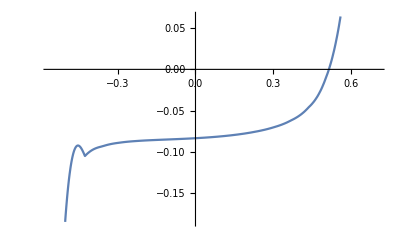

-0.0551888

```mathematica
func20p=Interpolation[{{-0.56,-0.681318360191},{-0.49352631578947376,-0.146893499351},{-0.42705263157894746,-0.104921712115},{-0.3605789473684211,-0.093289904125},{-0.2941052631578948,-0.0887845314327},{-0.22763157894736852,-0.086721236909},{-0.16115789473684217,-0.0855801537739},{-0.09468421052631587,-0.0847185691906},{-0.028210526315789575,-0.0837982818834},{0.03826315789473678,-0.0825942891348},{0.10473684210526302,-0.0809104776651},{0.17121052631578937,-0.0785187859121},{0.23768421052631572,-0.075072443863},{0.30415789473684185,-0.0699134081944},{0.3706315789473683,-0.0615425251388},{0.43710526315789466,-0.0459154376538},{0.5035789473684209,-0.0103686106369},{0.5700526315789471,0.0845091851321},{0.6365263157894736,0.314074066525},{0.7029999999999998,0.689960312954}}];
Plot[func20p[pz],{pz,-0.56,0.703}]
NIntegrate[func20p[pz],{pz,-0.56,0.703}]
```

If we increase the number of sites to 800, then the result gets different by several percents

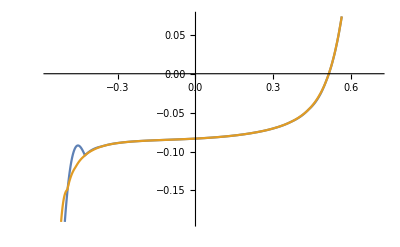

-0.0518362

1.0538

```mathematica
func40p800sites=Interpolation[{{-0.56,-0.681305936996},{-0.5276153846153847,-0.234730097613},{-0.4952307692307693,-0.149173057668},{-0.4628461538461539,-0.119774922409},{-0.43046153846153856,-0.105932983557},{-0.3980769230769231,-0.0983539127888},{-0.36569230769230776,-0.093828558127},{-0.3333076923076924,-0.0909720419396},{-0.300923076923077,-0.0890935840387},{-0.2685384615384616,-0.0878165179944},{-0.23615384615384621,-0.0869148830425},{-0.20376923076923087,-0.0862491261493},{-0.17138461538461547,-0.0857263898958},{-0.13900000000000012,-0.0852822693549},{-0.10661538461538472,-0.0848698844847},{-0.07423076923076927,-0.0844533444579},{-0.04184615384615398,-0.0840036417166},{-0.009461538461538632,-0.0834959198243},{0.022923076923076824,-0.082907506473},{0.05530769230769228,-0.0822163257582},{0.08769230769230763,-0.0813994068072},{0.12007692307692297,-0.0804312336895},{0.15246153846153832,-0.0792816468868},{0.18484615384615377,-0.0779128983241},{0.21723076923076912,-0.0762752406202},{0.24961538461538446,-0.074300009961},{0.2819999999999998,-0.0718883614334},{0.31438461538461526,-0.0688922651352},{0.3467692307692306,-0.0650812977926},{0.37915384615384595,-0.060082569913},{0.4115384615384615,-0.0532695566952},{0.44392307692307686,-0.0435478352539},{0.4763076923076921,-0.0289560813611},{0.5086923076923076,-0.00597131301751},{0.5410769230769228,0.0314450296607},{0.5734615384615385,0.0923682404784},{0.6058461538461537,0.187013029536},{0.6382307692307689,0.322225563213},{0.6706153846153846,0.496265391245},{0.7029999999999998,0.689961514563}}];
Plot[{func20p[pz],func40p800sites[pz]},{pz,-0.56,0.703}]
NIntegrate[func40p800sites[pz],{pz,-0.56,0.703}]
%/-ϵ0R/.BBLSet2
```

#### Now, let us deform the boundary: the velocity integral is quite different from -b_0/2!

We have deformed the boundary by rescaling b_0 in the on-site Hamiltonian of i=0 lattice site by 10 times

400 lattice sites

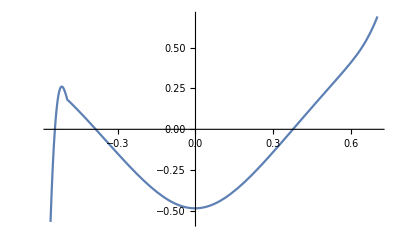

2.24788

```mathematica
func40pDefBound=Interpolation[{{-0.56,-0.566378341837},{-0.5276153846153847,0.223505234793},{-0.4952307692307693,0.181299616956},{-0.4628461538461539,0.131237630273},{-0.43046153846153856,0.0777253469597},{-0.3980769230769231,0.0222249102808},{-0.36569230769230776,-0.0343710024655},{-0.3333076923076924,-0.0913449057814},{-0.300923076923077,-0.147996587959},{-0.2685384615384616,-0.203560337684},{-0.23615384615384621,-0.257191315229},{-0.20376923076923087,-0.307904419846},{-0.17138461538461547,-0.354576519326},{-0.13900000000000012,-0.395924553798},{-0.10661538461538472,-0.430702419011},{-0.07423076923076927,-0.457496454925},{-0.04184615384615398,-0.475161765425},{-0.009461538461538632,-0.482832797546},{0.022923076923076824,-0.4801011102},{0.05530769230769228,-0.467082373724},{0.08769230769230763,-0.444406104261},{0.12007692307692297,-0.413090059952},{0.15246153846153832,-0.374381108574},{0.18484615384615377,-0.329597547486},{0.21723076923076912,-0.280009519604},{0.24961538461538446,-0.22674597775},{0.2819999999999998,-0.170862135884},{0.31438461538461526,-0.113177899719},{0.3467692307692306,-0.0543943887308},{0.37915384615384595,0.00491292962473},{0.4115384615384615,0.0642950883001},{0.44392307692307686,0.123447303666},{0.4763076923076921,0.18213663063},{0.5086923076923076,0.24040737468},{0.5410769230769228,0.298595322582},{0.5734615384615385,0.357627242818},{0.6058461538461537,0.41958341185},{0.6382307692307689,0.489352229038},{0.6706153846153846,0.576371710128},{0.7029999999999998,0.690432924662}}];
Plot[func40pDefBound[pz],{pz,-0.56,0.703}]
NIntegrate[func40pDefBound[pz],{pz,-0.56,0.703}];
%/-ϵ0R/.BBLSet2
```

## Set-4

```mathematica
NSolve[{(b0/bz Sin[pz])^2+2Cos[pz](1+M0)-(1+(1+M0)^2-(bz^2-b0^2)/4)==0}/.bz->3/.b0->0.2/.M0->0.,{pz}]

BBLSet4={bz->3,b0->0.2,M0->0.,pzWR->pz/.%[[1]],ϵ0R->-0.2/3.Sin[pz]/.%[[1]],ϵ0L->+0.2/3.Sin[pz]/.%[[1]]}
Subscript[vSet4, perp]=Sqrt[4(bz^2-b0^2)/(bz^2-4 ϵ0R^2)]/.BBLSet4
Subscript[vSet4, parallel]=1/(2(bz^2-4 ϵ0R^2))Sqrt[2^2(4ϵ0R(1+M0)Sin[pzWR]+b0 bz Cos[pzWR])^2+4(bz^2-4 ϵ0R^2)(4(Sin[pzWR])^2(1+M0)^2-b0^2(Cos[pzWR])^2)]/.BBLSet4
vzcorrSet4=(-(4ϵ0R(1+M0)Sin[pzWR]+b0 bz Cos[pzWR]))/(bz^2-4 ϵ0R^2)/.BBLSet4
vzArcTotSet4=-2.×10^-3;
tRSet4=-Sqrt[(Subscript[vSet4, parallel]-(vzcorrSet4-vzArcTotSet4))/(Subscript[vSet4, parallel]+(vzcorrSet4-vzArcTotSet4))]
tLSet4=-tRSet4;
lBSet4=40.;
dPzMinSet4=ϵ0R/(Subscript[vSet4, parallel]-vzcorrSet4)/.BBLSet4
dPzMaxSet4=-ϵ0L/(Subscript[vSet4, parallel]+vzcorrSet4)/.BBLSet4
BBLSet4={BBLSet4,Subscript[v, parallel]->Subscript[vSet4, parallel],Subscript[v, perp]->Subscript[vSet4, perp],vzcorr->vzcorrSet4,tR->tRSet4,tL->tLSet4}//Flatten
```

NSolve::ifun: Inverse functions are being used by NSolve, so some solutions may not be found; use Reduce for complete solution information.

{{pz→-1.69329},{pz→0.-6.80267 ⅈ},{pz→0.+6.80267 ⅈ},{pz→1.69329}}

{bz→3,b0→0.2,M0→0.,pzWR→-1.69329,ϵ0R→0.0661671,ϵ0L→-0.0661671}

1.99749

0.663321

0.037406

-0.942257

0.105713

0.0944264

{bz→3,b0→0.2,M0→0.,pzWR→-1.69329,ϵ0R→0.0661671,ϵ0L→-0.0661671,v_parallel→0.663321,v_perp→1.99749,vzcorr→0.037406,tR→-0.942257,tL→0.942257}

```mathematica
ϵ0R-Subscript[vSet4, perp] Sqrt[2]/40/.BBLSet4
```

-0.00445499

1.61264

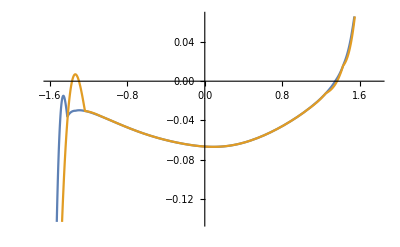

1.34524

```mathematica
FermiVelocityZSet4=Interpolation[{{-1.59,-0.659668439332},{-1.4126315789473685,-0.0355845535685},{-1.2352631578947368,-0.030390790267},{-1.0578947368421052,-0.036337312534},{-0.8805263157894737,-0.0437937235366},{-0.7031578947368421,-0.0507892260833},{-0.5257894736842106,-0.0566729200576},{-0.34842105263157896,-0.0612872243771},{-0.17105263157894735,-0.0646934142286},{0.006315789473684275,-0.0667072074137},{0.1836842105263159,-0.0665979338556},{0.3610526315789473,-0.0637354544138},{0.5384210526315789,-0.0581718482404},{0.7157894736842108,-0.0502864427404},{0.8931578947368422,-0.0403316536988},{1.070526315789474,-0.0281496486692},{1.2478947368421054,-0.0122944777611},{1.4252631578947368,0.0157313201633},{1.6026315789473686,0.129630416988},{1.78,0.632727275477}}];
(*Plot[FermiVelocityZSet4[pz],{pz,-1.59,1.78}]*)
Integrate[FermiVelocityZSet4[pz],{pz,-1.59,1.78}];
%/-ϵ0R/.BBLSet4

FermiVelocityZSet4finer=Interpolation[{{-1.59,-0.659668439332},{-1.5035897435897436,-0.0671456429199},{-1.4171794871794872,-0.0362108665412},{-1.330769230769231,-0.0301337538541},{-1.2443589743589745,-0.0302180748009},{-1.157948717948718,-0.0325417454959},{-1.0715384615384616,-0.0357838468262},{-0.9851282051282052,-0.0393765595568},{-0.8987179487179487,-0.04303264129},{-0.8123076923076923,-0.0465891601475},{-0.7258974358974359,-0.0499469289394},{-0.6394871794871796,-0.0530452306894},{-0.5530769230769232,-0.0558504168335},{-0.4666666666666668,-0.0583504313564},{-0.3802564102564103,-0.0605499859459},{-0.29384615384615387,-0.0624621740844},{-0.2074358974358974,-0.0640936930967},{-0.12102564102564117,-0.0654254964401},{-0.03461538461538449,-0.0663983693265},{0.051794871794871744,-0.0669166780417},{0.1382051282051282,-0.0668745189952},{0.22461538461538444,-0.0661905488265},{0.3110256410256409,-0.0648298543914},{0.3974358974358976,-0.0628029044711},
{0.4838461538461536,-0.060148934114},{0.57025641025641,-0.056916876024},{0.6566666666666665,-0.0531517810442},{0.7430769230769234,-0.0488871836552},{0.8294871794871794,-0.0441402129227},{0.9158974358974359,-0.0389052040255},{1.0023076923076923,-0.0331406978501},{1.0887179487179488,-0.0267405718141},{1.1751282051282053,-0.0194684371135},{1.2615384615384617,-0.0107937142091},{1.3479487179487177,0.000563198737328},{1.4343589743589742,0.0180762110417},{1.520769230769231,0.052461471886},{1.607179487179487,0.136224055897},{1.6935897435897436,0.32821992328},{1.78,0.632727275477}}];
Plot[{FermiVelocityZSet4finer[pz],FermiVelocityZSet4[pz]},{pz,-1.59,1.78}]
Integrate[FermiVelocityZSet4finer[pz],{pz,-1.59,1.78}];
%/-ϵ0R/.BBLSet4
```

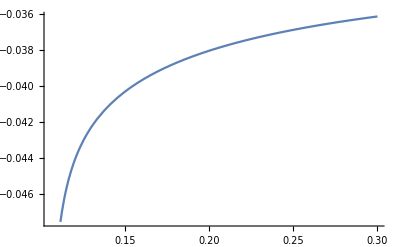

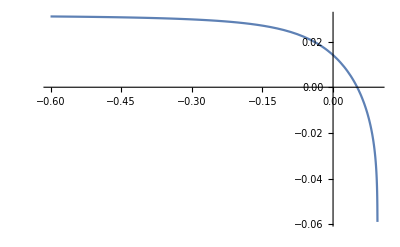

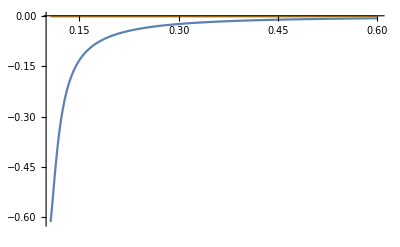

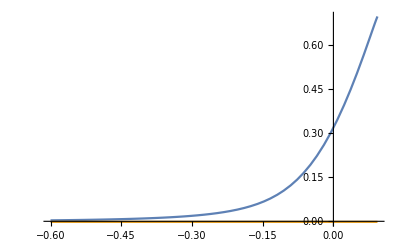

```mathematica
DispersionRSet4=Sqrt[2]tR Subscript[v, perp]/lBSet4 ParabolicCylinderD[lBSet4^2/Subscript[v, perp]^2(δϵ^2-Subscript[v, parallel]^2 dPz^2)/2,Sqrt[2]py lBSet4]+(δϵ+Subscript[v, parallel] dPz)ParabolicCylinderD[lBSet4^2/Subscript[v, perp]^2(δϵ^2-Subscript[v, parallel]^2 dPz^2)/2-1,Sqrt[2]py lBSet4]/.δϵ->ϵ-ϵ0R-vzcorr dPz/.BBLSet4;
DispersionLSet4=Sqrt[2](-1/tL)Subscript[v, perp]/lBSet4 ParabolicCylinderD[lBSet4^2/Subscript[v, perp]^2(δϵ^2-Subscript[v, parallel]^2 dPz^2)/2,Sqrt[2]py lBSet4]+(δϵ-Subscript[v, parallel] dPz)ParabolicCylinderD[lBSet4^2/Subscript[v, perp]^2(δϵ^2-Subscript[v, parallel]^2 dPz^2)/2-1,Sqrt[2]py lBSet4]/.δϵ->ϵ-ϵ0L-vzcorr dPz/.BBLSet4;
pyFermiRSet4[dPzVar_]:=py/.FindRoot[DispersionRSet4/.dPz->dPzVar/.ϵ->0,{py,-0.1}]
Plot[pyFermiRSet4[dPzVar],{dPzVar,dPzMinSet4+10^-4,0.3}]
pyFermiLSet4[dPzVar_]:=py/.FindRoot[DispersionLSet4/.dPz->dPzVar/.ϵ->0,{py,-0.01}]
Plot[pyFermiLSet4[dPzVar],{dPzVar,-0.6,dPzMaxSet4-10^-4},PlotRange->All]
dEOdPzRSet4[dPzVar_,dPzIncrement_]:=ϵ/dPzIncrement/.FindRoot[DispersionRSet4/.dPz->(dPzVar+dPzIncrement)/.py->pyFermiRSet4[dPzVar],{ϵ,0}]
Plot[{dEOdPzRSet4[dPzVar,0.001],-(1-tRSet4^2)/(1+tRSet4^2)Subscript[vSet4, parallel]+vzcorrSet4},{dPzVar,dPzMinSet4+10^-3,0.6},PlotRange->All]
dEOdPzLSet4[dPzVar_,dPzIncrement_]:=ϵ/dPzIncrement/.FindRoot[DispersionLSet4/.dPz->(dPzVar+dPzIncrement)/.py->pyFermiLSet4[dPzVar],{ϵ,0}]
Plot[{dEOdPzLSet4[dPzVar,-0.001],-(1-tLSet4^2)/(1+tLSet4^2)Subscript[vSet4, parallel]+vzcorrSet4},{dPzVar,-0.6,dPzMaxSet4-10^-3},PlotRange->All]
```

The calculation of the I^z prefactor is based on separability assumption, which seems to hold well, for the non-deformed boundary

```mathematica
dPzCutRSet4=0.3;
dPzCutLSet4=-0.3;
IZRCutSet4=Quiet@NIntegrate[dEOdPzRSet4[dPzVar,10^-3],{dPzVar,dPzMinSet4+10^-3,dPzCutRSet4}];
IZLCutSet4=Quiet@NIntegrate[dEOdPzLSet4[dPzVar,-10^-3],{dPzVar,dPzCutLSet4,dPzMaxSet4-10^-3}];
IZRCutSet4+IZLCutSet4+(ϵ0L+(-(1-tL^2)/(1+tL^2)Subscript[v, parallel]+vzcorr)dPzCutLSet4)-(ϵ0R+(-(1-tR^2)/(1+tR^2)Subscript[v, parallel]+vzcorr)dPzCutRSet4)/.BBLSet4;
%/-ϵ0R/.BBLSet4
```

1.14747

### Deformation of the boundary gives a different answer

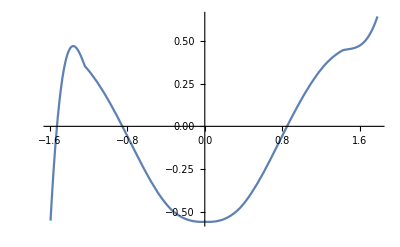

2.25994

```mathematica
funcSet4DefBound=Interpolation[{{-1.59,-0.553373762004},{-1.4126315789473685,0.427655194922},{-1.2352631578947368,0.352347181816},{-1.0578947368421052,0.214907897289},{-0.8805263157894737,0.0344924962145},{-0.7031578947368421,-0.164817156884},{-0.5257894736842106,-0.35113817503},{-0.34842105263157896,-0.48681827025},{-0.17105263157894735,-0.548763939988},{0.006315789473684275,-0.560206860005},{0.1836842105263159,-0.547572538573},{0.3610526315789473,-0.480247710263},{0.5384210526315789,-0.339023199572},{0.7157894736842108,-0.149673382621},{0.8931578947368422,0.0503382527303},{1.070526315789474,0.230114199321},{1.2478947368421054,0.367122844837},{1.4252631578947368,0.447042101902},{1.6026315789473686,0.476083932167},{1.78,0.64481234413}}];
Plot[funcSet4DefBound[pz],{pz,-1.59,1.78}]
NIntegrate[funcSet4DefBound[pz],{pz,-1.59,1.78}];
%/-ϵ0R/.BBLSet4
```

## Set-5

```mathematica
NSolve[{(b0/bz Sin[pz])^2+2Cos[pz](1+M0)-(1+(1+M0)^2-(bz^2-b0^2)/4)==0}/.bz->3/.b0->0.1/.M0->0.,{pz}]

BBLSet5={bz->3,b0->0.1,M0->0.,pzWR->pz/.%[[1]],ϵ0R->-0.1/3.Sin[pz]/.%[[1]],ϵ0L->+0.1/3.Sin[pz]/.%[[1]]}
Subscript[vSet5, perp]=Sqrt[4(bz^2-b0^2)/(bz^2-4 ϵ0R^2)]/.BBLSet5
Subscript[vSet5, parallel]=1/(2(bz^2-4 ϵ0R^2))Sqrt[2^2(4ϵ0R(1+M0)Sin[pzWR]+b0 bz Cos[pzWR])^2+4(bz^2-4 ϵ0R^2)(4(Sin[pzWR])^2(1+M0)^2-b0^2(Cos[pzWR])^2)]/.BBLSet5
vzcorrSet5=(-(4ϵ0R(1+M0)Sin[pzWR]+b0 bz Cos[pzWR]))/(bz^2-4 ϵ0R^2)/.BBLSet5
vzArcTotSet5=-0.00085;
tRSet5=-Sqrt[(Subscript[vSet5, parallel]-(vzcorrSet5-vzArcTotSet5))/(Subscript[vSet5, parallel]+(vzcorrSet5-vzArcTotSet5))]
tLSet5=-tRSet5;
lBSet5=80.;
dPzMinSet5=ϵ0R/(Subscript[vSet5, parallel]-vzcorrSet5)/.BBLSet5
dPzMaxSet5=-ϵ0L/(Subscript[vSet5, parallel]+vzcorrSet5)/.BBLSet5
BBLSet5={BBLSet5,Subscript[v, parallel]->Subscript[vSet5, parallel],Subscript[v, perp]->Subscript[vSet5, perp],vzcorr->vzcorrSet5,tR->tRSet5,tL->tLSet5}//Flatten
```

NSolve::ifun: Inverse functions are being used by NSolve, so some solutions may not be found; use Reduce for complete solution information.

{{pz→-1.69542},{pz→0.-8.18876 ⅈ},{pz→0.+8.18876 ⅈ},{pz→1.69542}}

{bz→3,b0→0.1,M0→0.,pzWR→-1.69542,ϵ0R→0.0330748,ϵ0L→-0.0330748}

1.99937

0.66191

0.0187383

-0.970832

0.0514246

0.0485931

{bz→3,b0→0.1,M0→0.,pzWR→-1.69542,ϵ0R→0.0330748,ϵ0L→-0.0330748,v_parallel→0.66191,v_perp→1.99937,vzcorr→0.0187383,tR→-0.970832,tL→0.970832}

#### Direct integration

```mathematica
FermiVelocityZSet5=Interpolation[{...}];
(*Plot[FermiVelocityZSet5[pz],{pz,-1.64,1.74}]*)
Integrate[FermiVelocityZSet5[pz],{pz,-1.64,1.74}];
%/-ϵ0R/.BBLSet5
```

#### Effective theory in separable approximation

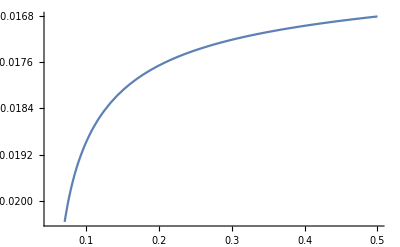

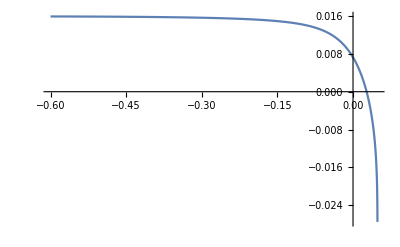

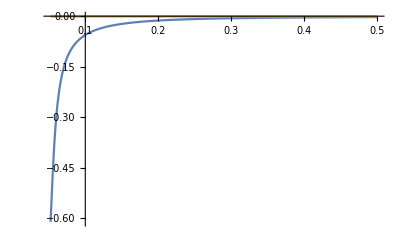

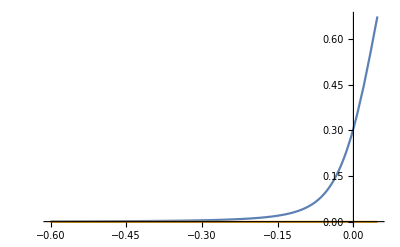

```mathematica
DispersionRSet5=Sqrt[2]tR Subscript[v, perp]/lBSet5 ParabolicCylinderD[lBSet5^2/Subscript[v, perp]^2(δϵ^2-Subscript[v, parallel]^2 dPz^2)/2,Sqrt[2]py lBSet5]+(δϵ+Subscript[v, parallel] dPz)ParabolicCylinderD[lBSet5^2/Subscript[v, perp]^2(δϵ^2-Subscript[v, parallel]^2 dPz^2)/2-1,Sqrt[2]py lBSet5]/.δϵ->ϵ-ϵ0R-vzcorr dPz/.BBLSet5;
DispersionLSet5=Sqrt[2](-1/tL)Subscript[v, perp]/lBSet5 ParabolicCylinderD[lBSet5^2/Subscript[v, perp]^2(δϵ^2-Subscript[v, parallel]^2 dPz^2)/2,Sqrt[2]py lBSet5]+(δϵ-Subscript[v, parallel] dPz)ParabolicCylinderD[lBSet5^2/Subscript[v, perp]^2(δϵ^2-Subscript[v, parallel]^2 dPz^2)/2-1,Sqrt[2]py lBSet5]/.δϵ->ϵ-ϵ0L-vzcorr dPz/.BBLSet5;
pyFermiRSet5[dPzVar_]:=py/.FindRoot[DispersionRSet5/.dPz->dPzVar/.ϵ->0,{py,-0.05,0.02},Method->"Brent"]
Plot[pyFermiRSet5[dPzVar],{dPzVar,dPzMinSet5+10^-4,0.5}]
pyFermiLSet5[dPzVar_]:=py/.FindRoot[DispersionLSet5/.dPz->dPzVar/.ϵ->0,{py,-0.05,0.02},Method->"Brent"]
Plot[pyFermiLSet5[dPzVar],{dPzVar,-0.6,dPzMaxSet5-10^-4},PlotRange->All]
dEOdPzRSet5[dPzVar_,dPzIncrement_]:=ϵ/dPzIncrement/.FindRoot[DispersionRSet5/.dPz->(dPzVar+dPzIncrement)/.py->pyFermiRSet5[dPzVar],{ϵ,0}]
Plot[{dEOdPzRSet5[dPzVar,0.001],-(1-tRSet5^2)/(1+tRSet5^2)Subscript[vSet5, parallel]+vzcorrSet5},{dPzVar,dPzMinSet5+10^-3,0.5},PlotRange->All]
dEOdPzLSet5[dPzVar_,dPzIncrement_]:=ϵ/dPzIncrement/.FindRoot[DispersionLSet5/.dPz->(dPzVar+dPzIncrement)/.py->pyFermiLSet5[dPzVar],{ϵ,0}]
Plot[{dEOdPzLSet5[dPzVar,-0.001],-(1-tLSet5^2)/(1+tLSet5^2)Subscript[vSet5, parallel]+vzcorrSet5},{dPzVar,-0.6,dPzMaxSet5-10^-3},PlotRange->All]
```

```mathematica
dPzCutRSet5=0.3;
dPzCutLSet5=-0.3;
IZRCutSet5=Quiet@NIntegrate[dEOdPzRSet5[dPzVar,10^-3],{dPzVar,dPzMinSet5+10^-3,dPzCutRSet5}];
IZLCutSet5=Quiet@NIntegrate[dEOdPzLSet5[dPzVar,-10^-3],{dPzVar,dPzCutLSet5,dPzMaxSet5-10^-3}];
IZRCutSet5+IZLCutSet5+(ϵ0L+(-(1-tR^2)/(1+tR^2)Subscript[v, parallel]+vzcorr)dPzCutLSet5)-(ϵ0R+(-(1-tR^2)/(1+tR^2)Subscript[v, parallel]+vzcorr)dPzCutRSet5)/.BBLSet5;
%/-ϵ0R/.BBLSet5
```

1.17473